```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Get["LatticePhyllotaxis.wl"];
Get["DiskStacking.wl"];
```

### Do a short run

```mathematica
arena= <|"runNumber"->1
,"Tag"->"example-radius-34bis"
,"Run"->""
,"diskMax"-> 177
,"radiusFunctionParameters" -> {
<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1.7,
"zRange"-> 0.1|>
,<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.9,"zRange"->0.02|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.4/0.9,"zRange"->0.15|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.2/(0.4/0.9),"zRange"->0.15|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{21,34},cylinderLU={-0.01,0.1}]
|>;

shortExample = doOneRun[arena];
```

```mathematica
shortExample["ContactGraph"]
```

## Do a longer run

```mathematica
arenaLong = arena;
arenaLong["diskMax"]= ∞;
example = doOneRun[arenaLong];
```

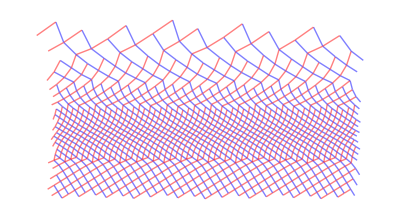

```mathematica
Graph[example["ContactGraph"],VertexLabels->None]
```

## Do multiple runs

To redo the  computation  corresponding  to  the  first  column  of  the  main  result  histogram  table  of  the  paper:

```mathematica
computeParastichyPairs[parameters_] := Module[{run,parastichyPair},
run = doOneRun[parameters];
run = DiskStacking`postRunExtractNonOverlappingChains[run];
parastichyPair = Last@Values@run["ParastichyPairs"];
(* nb the paper pooled all the parastichy numbers seen in  each run   - this example just takes the last one *)
parastichyPair
];
```

```mathematica
durhamRunParameters = <|
"Tag"->"rcp-upto55-durham",
"Noise"->0,
"radiusFunctionParameters" -> {
<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearReduction","rScale"-> 60,"rSlope"->0.01|>(* the paper took rScale = 60 so as to get to 34,55 ; choose rScale =6 for a quick test run  *)
,<|"Type"->"Constant","ApproximateChains"->1|> (* the paper took 10 of these *)
},
"Lattice"-> LatticePhyllotaxis`latticeOrthogonal[{0,1},{0,2}]
|>;

computeParastichyPairs[durhamRunParameters]
```

{34,55}

```mathematica
(* now try changing rSlope - which is the same as the r' of the paper - what are the final parastichy pairs as a function of rSlope ? 
In particular when is r' too large to allow Fibonacci transitions? 
What is the behaviour near the critical value? Probably noisy and not monotonic there 
 *)
```

## Run code

```mathematica
doOneRun[parameters_] := Module[{run},
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run=doMonitoredRun[run];
run
];

doMonitoredRun[run_] := Module[{res},
SeedRandom[run["Arena"]["Run"]];
res=run;
monitorRun= res["Arena"]["Run"];
monitorPP = <|"Noise"->res["Arena"]["Noise"],"rSlope"->res["Arena"]["rSlope"]|>;
res = DiskStacking`executeRun[res]; 
res 
];
```

```mathematica
doRunSets[parameterSets_] := Module[{res,abortCheck,runSets,timing},
abortCheck[parameterSet_] := CheckAbort[doOneRun[parameterSet],Print["Abort running ",parameterSet["Run"]]; Missing[parameterSet["Run"]]];
monitorRunTotal = Length[parameterSets];
monitorRunNumber= 0;
{timing,res}= Timing[Monitor[runSets=Map[(monitorRunNumber++;abortCheck[#]&),parameterSets],{monitorRunTotal,monitorRunNumber,monitorRun,monitorPP}];];
runSets
];
```

```mathematica
latestRadius[run_] := Last@Values[DiskStacking`runDisksRadius[run]];
latestCentre[run_] := Last@Values[DiskStacking`runDisksHeight[run]];

readyRunFromParameter[lastRun_,experimentParameters_] := Module[{runParameters,run,arena},

(* set defaults *)
runParameters= <|
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1}],
"zMax"->Missing[],
"runNumber"->1,
"diskMax"->∞,
"PostFixChains"->0,
"Run"->"",
"Noise"->Missing[]
|>;

runParameters= Append[runParameters,experimentParameters];
run=lastRun;


run["Arena"] = createRFunctionArena[{latestCentre[run],latestRadius[run]},runParameters];
run["Arena"]["GitHub"] = "Example";
run
];


createRFunctionArena[{initialZ_ ,initialRadius_},runParameters_] := Module[{calcfunctionParameters,inverseLinearDecreaseFunctionParameters,linearFunctionParameters,constFunctionParameters,
arena,sectionStartRadius,sectionStartZ,functionCount,rFunctionPieces,lookup,z},

calcfunctionParameters[functionParameter_] := Switch[functionParameter["Type"],
"Constant",constFunctionParameters[functionParameter]
,
"LinearReduction",linearFunctionParameters[functionParameter]
,
"LinearCircumferenceIncrease",inverseLinearDecreaseFunctionParameters[functionParameter]
,
_,
 Print["Type not set ",functionParameter];Abort[];
];
inverseLinearDecreaseFunctionParameters[functionParameter_] := Module[{res,circumferenceStart,circumferenceScale,rStart,circumferenceEnd,rEnd,zEnd,func},
circumferenceStart = 1/sectionStartRadius;
circumferenceEnd = circumferenceStart* functionParameter["circumferenceScale"];
zEnd = sectionStartZ+functionParameter["zRange"];
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"->  sectionStartRadius/functionParameter["circumferenceScale"]
,"rScale"-> 1/functionParameter["circumferenceScale"]
,"zStart"-> sectionStartZ
,"zEnd"-> zEnd|>
];
func = Function[{z},sectionStartRadius*(zEnd-sectionStartZ) / (-(z-zEnd) +(functionParameter["circumferenceScale"])*( z-sectionStartZ))];
res["rFunction"] = functionClosure[func];

sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
linearFunctionParameters[functionParameter_] := Module[{res,rStart,rEnd},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius,
"rEnd"-> sectionStartRadius/functionParameter["rScale"]
,"zStart"-> sectionStartZ|>
];
res = Append[res,linearFunctionProperties[ {res["rStart"],res["rEnd"]},res["rSlope"],sectionStartZ]];
sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
constFunctionParameters[functionParameter_] := Module[{res,finalRadius},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"-> sectionStartRadius
,"zStart"-> sectionStartZ
,"zEnd"-> sectionStartZ + functionParameter["ApproximateChains"]* 4* sectionStartRadius
|>];
res = Append[res,<|"rFunction"->Function[{z},Evaluate[sectionStartRadius]]|>];
sectionStartZ = res["zEnd"];
res
];


sectionStartZ =  initialZ;
sectionStartRadius = initialRadius;
functionCount = 1;

arena = runParameters;
arena["rFunctionList"] = Association@Map[functionCount++->calcfunctionParameters[#]&,arena["radiusFunctionParameters"]];

bq=KeyValueMap[{(lookup[#1]),#2["zStart"]<z<= #2["zEnd"]}&,arena["rFunctionList"]];
bq = Prepend[bq,{arena["rFunctionList"][1]["rStart"],z<= arena["rFunctionList"][1]["zStart"]}];
bq = Append[bq,{Last[arena["rFunctionList"]]["rEnd"],z > (Last[arena["rFunctionList"]])["zEnd"]}];

rFunctionPieces = bq  /. lookup[i_] :> arena["rFunctionList"][i]["rFunction"][z];

arena["rFunctionPieces"] = rFunctionPieces ;
arena["rFunction"] := Function[{zq},Piecewise[arena["rFunctionPieces"]]/. z-> zq]; 
arena["zMax"] = (Last[arena["rFunctionList"]])["zEnd"]; 
arena

];


linearFunctionProperties[ {rStart_,rEnd_},rSlope_,zStart_,power_:1] := Module[{zSlopeRange,zEnd,func,rDash,scaler},
rDash = -rSlope;
scaler = Sign[rDash]*(Abs[(zEnd-zStart) * rDash] )^ (power-1);
zEnd = zStart + ( (rEnd-rStart))/rDash ;

func = Function[{z},rStart+(((z-zStart) * Abs[rDash])^power)/scaler];
func  = functionClosure[func];
<|"rFunction"-> func, "zEnd"-> zEnd|>
]


functionClosure[f_] := Function[{z$},Evaluate[f[[2]]]]
```